```mathematica
SetOptions[EvaluationNotebook[],CellEpilog:>SelectionMove[NextCell[CellStyle->"Input"],All,Cell]]
```

```mathematica
s[p_,q_,d_]:=s[p,q,d]=If[d>=p+q,Import[NotebookDirectory[]<>"./idempotents_db/primitive_"<>ToString[p]<>"_"<>ToString[q]<>".txt"],Import[NotebookDirectory[]<>"./idempotents_db/primitive_"<>ToString[p]<>"_"<>ToString[q]<>"_"<>ToString[d]<>".txt"]];
```

```mathematica
(* Pares Sage output into Mathematica *)
Parse[s_]:=Module[{t,λs,εs},
(* Rmove the first and last curcly brace *)
t=StringTake[s,{2,-2}];
(* Fix the brackets of B *)
t=StringReplace[t,{"{{"->"[{","}}"->"}]"}];
(* Add extra colons before path labels and convert all braces to curly *)
t=StringReplace[t,{"((["->":{{[","(["->"{[","]))"->"]}}","])"->"]}"}];
(* Replace []->{} and [1,2]->{1,2} *)
t=StringReplace[t,{"[]"->"{}"}];
t=StringReplace[t,{StringExpression["[",i:NumberString]:>"{"~~i}];
t=StringReplace[t,{StringExpression[i:NumberString,"]"]:>i~~"}"}];
(* Remove commas after idempotents *)
t=StringReplace[t,", :"->" : "];
(* Split the string at colons *)
t=StringSplit[t,":"];
(* Mathematica expression *)
t=ToExpression[t];
(* Final vertex on a path and its idempotent *)
{λs,εs}=Partition[t,2]ᵀ;
λs=Last/@λs;
{λs,εs}
];
```

```mathematica
(* Elementary rank-1 matrix *)
ketbra[s_,t_,{p_,q_,d_}]:=SparseArray[{{FromDigits[s,d],FromDigits[t,d]}+1->1},{d^(p+q),d^(p+q)}]
```

```mathematica
(* Converts a diagram into a Matrix *)
ψ[diagram__,{p_,q_,d_}]:=ψ[diagram,{p,q,d}]=Module[{δ,ip,in,is,range,s},
δ=Times@@(KroneckerDelta[i[#⟦1⟧],i[#⟦2⟧]]&/@{diagram});
ip=Table[i[k],{k,p+q}];
in=Table[i[-k],{k,p+q}];
is=Join[in,ip];
range=Sequence@@({#,0,d-1}&/@is);
Sum[δ*ketbra[in,ip,{p,q,d}],Evaluate[range]]
];
```

```mathematica
(* Converts a linear combination of diagrams into a matrix *)
ToMatrix[lst_List,pqd_]:=ToMatrix[#,pqd]&/@lst;
ToMatrix[expr_,{p_,q_,d_}]:=Normal[expr/.B[lst__]:>ψ[lst,{p,q,d}]]/.z->d;
```

```mathematica
(* Finds the 1-eingevectors of a projector *)
Vecs[M_]:=Module[{λs,vs},
{λs,vs}=Eigensystem@M;
Orthogonalize@Pick[vs,λs,1]
];
```

```mathematica
(* Direct sum of a list of matrices *)
DirectSum[lst_]:=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@lst];
(* Big SWAP *)
SWAP[dAs_List,dBs_List]:=DirectSum[SWAP@@@({dAs,dBs}ᵀ)];
(* Swaps systems of dimension dA and dB *)
SWAP[0,_]=Nothing;
SWAP[_,0]=Nothing;
SWAP[dA_,dB_]:=SparseArray[Join@@Table[{a+b*dA,a*dB+b}+1->1,{a,0,dA-1},{b,0,dB-1}],{dA*dB,dA*dB}];
```

```mathematica
(* Extract one of each blocks in Schur basis *)
Blocks[S_,{dB_,dU_}]:=Module[{pivot,len,runs},
pivot=Prepend[Most@Accumulate[Times@@@({dB,dU}ᵀ)],0];
len=Range/@dB;
runs=pivot+len;
S⟦#,#⟧&/@runs
];
```

```mathematica
{p,q,d}={1,3,2};
```

```mathematica
(* Print error messages *)
Test[b_,txt_]:=If[Not[b],Print[Style[txt,{Red,Bold}]]];
(* Sort the diagram description to make it canonical *)
SortB[σ_]:=Sort@Map[Sort,σ,1];

(*Generate Walled Brauer Algebra basis*)
FlipPair[pair_,p_]:=Sort@(If[Abs[#]>p,-#,#]&/@pair);
WalledBrauerBasis[p_,q_]:=B[Sequence@@#]&/@Map[FlipPair[#,p]&,FoldList[ReplacePart[#1,#2->{-#2,#1[[#2]]}]&,#,Range[p+q]][[-1]]&/@Permutations[Range[p+q]],{2}];
```

```mathematica
(* Parse the idempotents *)
{λs,εs}=Parse[s[p,q,d]];
(* Locations of distinct diagrams *)
distinct=Sort[Position[λs,#,1,1]⟦1,1⟧&/@Union[λs]];
(* Dimensions of Brauer registers *)
dB=(λs/.Rule@@@Tally[λs])⟦distinct⟧;
(* Idempotent matrices *)
Πs=ToMatrix[εs,{p,q,d}];
(* Idempotent ranks *)
rs=MatrixRank/@Πs;
Test[Total[rs]==d^(p+q),"Ranks of idempotents don't sum to d^(p + q)"]
(* Dimensions of unitary register *)
dU=rs⟦distinct⟧;
Test[dB.dU==d^(p+q),"Block dimensions don't sum to d^(p + q)"]
(* Schur transform *)
U=Join@@(Vecs/@Πs);
Test[U.Uᵀ==IdentityMatrix[d^(p+q)],"U not unitary"]
(* Total dimension *)
d^(p+q)
(* Delete zeros from dU and dB for future*)
zeroes = Position[dU,0];
dB=Delete[dB,zeroes ]
dU=Delete[dU,zeroes ]
```

16

{1,3,2}

{5,3,1}

```mathematica
(* Linear combination of diagrams *)
Bs=DeleteCases[Sort@Variables[εs],z];
Bs2=SortB/@WalledBrauerBasis[p,q];
TableForm@Bs;
Sum[Subscript[a, i](εs[[i]]/.z->d),{i,1,Length@εs}];
sum=Sum[Subscript[b, i] Bs2⟦i⟧,{i,1,Length@Bs2}];
M=ToMatrix[sum,{p,q,d}];
MatrixForm@M;
```

```mathematica
kerSol=Solve[(#==0)&/@(Flatten@M)][[1]]
```

{b_6→-b_1-b_2-b_3-b_4-b_5,b_8→-b_1-b_2-b_7,b_11→-b_3-b_5-b_9,b_12→b_1+b_2+b_3+b_5-b_10,b_14→-b_3-b_4-b_13,b_15→-b_1-b_3-b_7-b_9-b_13,b_16→b_1+b_3+b_7-b_10+b_13,b_17→b_1+b_2+2 b_3+b_4+b_5+b_7+b_9+b_13,b_18→-b_1-b_2-b_3-b_5-b_7+b_10-b_13,b_20→b_1+b_2+b_3+b_4-b_19,b_21→b_1+b_3+b_7+b_9-b_19,b_22→-2 b_1-b_2-b_3-b_7+b_10+b_19,b_23→-b_1-b_2-b_3-b_4-b_7-b_9+b_19,b_24→b_1+b_2+b_7-b_10-b_19}

```mathematica
Keys[kerSol]
```

{b_6,b_8,b_11,b_12,b_14,b_15,b_16,b_17,b_18,b_20,b_21,b_22,b_23,b_24}

```mathematica
Complement[Variables[sum/.kerSol],Bs2]
sum/.kerSol//Simplify
```

{b_1,b_2,b_3,b_4,b_5,b_7,b_9,b_10,b_13,b_19}

B[{-4,4},{-3,3},{-2,2},{-1,1}] b_1+B[{-4,3},{-3,4},{-2,2},{-1,1}] b_2+B[{-4,4},{-3,2},{-2,3},{-1,1}] b_3+B[{-4,3},{-3,2},{-2,4},{-1,1}] b_4+B[{-4,2},{-3,4},{-2,3},{-1,1}] b_5-B[{-4,2},{-3,3},{-2,4},{-1,1}] (b_1+b_2+b_3+b_4+b_5)+B[{-4,4},{-3,3},{-2,-1},{1,2}] b_7-B[{-4,3},{-3,4},{-2,-1},{1,2}] (b_1+b_2+b_7)+B[{-4,4},{-3,2},{-2,-1},{1,3}] b_9-B[{-4,2},{-3,4},{-2,-1},{1,3}] (b_3+b_5+b_9)+B[{-4,2},{-3,3},{-2,-1},{1,4}] (b_1+b_2+b_3+b_5-b_10)+B[{-4,3},{-3,2},{-2,-1},{1,4}] b_10+B[{-4,4},{-3,-1},{-2,3},{1,2}] b_13-B[{-4,3},{-3,-1},{-2,4},{1,2}] (b_3+b_4+b_13)-B[{-4,4},{-3,-1},{-2,2},{1,3}] (b_1+b_3+b_7+b_9+b_13)+B[{-4,2},{-3,-1},{-2,4},{1,3}] (b_1+b_2+2 b_3+b_4+b_5+b_7+b_9+b_13)+B[{-4,3},{-3,-1},{-2,2},{1,4}] (b_1+b_3+b_7-b_10+b_13)-B[{-4,2},{-3,-1},{-2,3},{1,4}] (b_1+b_2+b_3+b_5+b_7-b_10+b_13)+B[{-4,-1},{-3,3},{-2,4},{1,2}] (b_1+b_2+b_3+b_4-b_19)+B[{-4,-1},{-3,4},{-2,2},{1,3}] (b_1+b_3+b_7+b_9-b_19)-B[{-4,-1},{-3,2},{-2,4},{1,3}] (b_1+b_2+b_3+b_4+b_7+b_9-b_19)+B[{-4,-1},{-3,2},{-2,3},{1,4}] (b_1+b_2+b_7-b_10-b_19)-B[{-4,-1},{-3,3},{-2,2},{1,4}] (2 b_1+b_2+b_3+b_7-b_10-b_19)+B[{-4,-1},{-3,4},{-2,3},{1,2}] b_19

```mathematica
{Bs,Bs2}ᵀ//TableForm
```

B[{-4,-1},{-3,2},{-2,3},{1,4}] | B[{-4,4},{-3,3},{-2,2},{-1,1}]
B[{-4,-1},{-3,2},{-2,4},{1,3}] | B[{-4,3},{-3,4},{-2,2},{-1,1}]
B[{-4,-1},{-3,3},{-2,2},{1,4}] | B[{-4,4},{-3,2},{-2,3},{-1,1}]
B[{-4,-1},{-3,3},{-2,4},{1,2}] | B[{-4,3},{-3,2},{-2,4},{-1,1}]
B[{-4,-1},{-3,4},{-2,2},{1,3}] | B[{-4,2},{-3,4},{-2,3},{-1,1}]
B[{-4,-1},{-3,4},{-2,3},{1,2}] | B[{-4,2},{-3,3},{-2,4},{-1,1}]
B[{-4,2},{-3,-1},{-2,3},{1,4}] | B[{-4,4},{-3,3},{-2,-1},{1,2}]
B[{-4,2},{-3,-1},{-2,4},{1,3}] | B[{-4,3},{-3,4},{-2,-1},{1,2}]
B[{-4,2},{-3,3},{-2,-1},{1,4}] | B[{-4,4},{-3,2},{-2,-1},{1,3}]
B[{-4,2},{-3,3},{-2,4},{-1,1}] | B[{-4,3},{-3,2},{-2,-1},{1,4}]
B[{-4,2},{-3,4},{-2,-1},{1,3}] | B[{-4,2},{-3,4},{-2,-1},{1,3}]
B[{-4,2},{-3,4},{-2,3},{-1,1}] | B[{-4,2},{-3,3},{-2,-1},{1,4}]
B[{-4,3},{-3,-1},{-2,2},{1,4}] | B[{-4,4},{-3,-1},{-2,3},{1,2}]
B[{-4,3},{-3,-1},{-2,4},{1,2}] | B[{-4,3},{-3,-1},{-2,4},{1,2}]
B[{-4,3},{-3,2},{-2,-1},{1,4}] | B[{-4,4},{-3,-1},{-2,2},{1,3}]
B[{-4,3},{-3,2},{-2,4},{-1,1}] | B[{-4,3},{-3,-1},{-2,2},{1,4}]
B[{-4,3},{-3,4},{-2,-1},{1,2}] | B[{-4,2},{-3,-1},{-2,4},{1,3}]
B[{-4,3},{-3,4},{-2,2},{-1,1}] | B[{-4,2},{-3,-1},{-2,3},{1,4}]
B[{-4,4},{-3,-1},{-2,2},{1,3}] | B[{-4,-1},{-3,4},{-2,3},{1,2}]
B[{-4,4},{-3,-1},{-2,3},{1,2}] | B[{-4,-1},{-3,3},{-2,4},{1,2}]
B[{-4,4},{-3,2},{-2,-1},{1,3}] | B[{-4,-1},{-3,4},{-2,2},{1,3}]
B[{-4,4},{-3,2},{-2,3},{-1,1}] | B[{-4,-1},{-3,3},{-2,2},{1,4}]
B[{-4,4},{-3,3},{-2,-1},{1,2}] | B[{-4,-1},{-3,2},{-2,4},{1,3}]
B[{-4,4},{-3,3},{-2,2},{-1,1}] | B[{-4,-1},{-3,2},{-2,3},{1,4}]

```mathematica
P=SWAP[dB,dU];
S=P.U.M.Uᵀ.Pᵀ//Simplify;
MatrixForm@S;
blocks=Blocks[S,{dB,dU}]/.{{0}}->Nothing;
MatrixForm/@blocks
```

{(b_1+b_2+b_3+b_4+b_5+b_6),(1/3 (3 b_1-b_2+3 b_3-b_4-b_5-b_6+4 b_22+4 b_24) | 1/3 √2 (2 b_2+2 b_4-b_5-b_6+3 b_21+b_22+3 b_23+b_24) | √(2/3) (b_5+b_6+2 b_19+2 b_20+b_21+b_22+b_23+b_24)
1/3 √2 (2 b_2-b_4+2 b_5-b_6+3 b_16+3 b_18+b_22+b_24) | 1/6 (6 b_1+2 b_2-3 b_3-b_4-b_5+5 b_6+9 b_15+3 b_16+9 b_17+3 b_18+3 b_21+b_22+3 b_23+b_24) | (3 b_3+3 b_4+b_5+b_6+6 b_13+6 b_14+3 b_15+3 b_16+3 b_17+3 b_18+2 b_19+2 b_20+b_21+b_22+b_23+b_24)/(2 √3)
√(2/3) (b_4+b_6+2 b_10+2 b_12+b_16+b_18+b_22+b_24) | (3 b_3+b_4+3 b_5+b_6+6 b_9+2 b_10+6 b_11+2 b_12+3 b_15+b_16+3 b_17+b_18+3 b_21+b_22+3 b_23+b_24)/(2 √3) | 1/2 (2 b_1+2 b_2+b_3+b_4+b_5+b_6+4 b_7+4 b_8+2 b_9+2 b_10+2 b_11+2 b_12+2 b_13+2 b_14+b_15+b_16+b_17+b_18+2 b_19+2 b_20+b_21+b_22+b_23+b_24)),(1/2 (2 b_1+2 b_2-b_3-b_4-b_5-b_6+3 b_15+3 b_16-3 b_17-3 b_18+3 b_21+3 b_22-3 b_23-3 b_24) | 1/2 √3 (b_3-b_4+b_5-b_6+2 b_13-2 b_14+b_15-b_16-b_17+b_18+2 b_19-2 b_20+b_21-b_22-b_23+b_24)
1/2 √3 (b_3+b_4-b_5-b_6+2 b_9+2 b_10-2 b_11-2 b_12+b_15+b_16-b_17-b_18-b_21-b_22+b_23+b_24) | 1/2 (2 b_1-2 b_2+b_3-b_4-b_5+b_6+4 b_7-4 b_8+2 b_9-2 b_10-2 b_11+2 b_12+2 b_13-2 b_14+b_15-b_16-b_17+b_18-2 b_19+2 b_20-b_21+b_22+b_23-b_24))}

```mathematica
spq={{({{1}}),({{1, 0, 0}, {0, -1/2, (√3)/2}, {0, (√3)/2, 1/2}}),({{-1/2, (√3)/2}, {(√3)/2, 1/2}})},{({{1}}),({{-1/3, (2 √2)/3, 0}, {(2 √2)/3, 1/3, 0}, {0, 0, 1}}),({{1, 0}, {0, -1}})}};
```

```mathematica
subst
```

{b_2→b_4-b_5+b_6+b_10+b_12-b_16-b_18,b_3→b_4-b_5+b_6-b_9+b_10-b_11+b_12,b_7→-b_12+b_15-b_18+b_19+b_21,b_8→-b_4+b_5-b_10+b_16+b_17+2 b_18-b_19-b_21,b_13→b_9+b_10+b_16-b_19-b_21,b_14→-b_4+b_5-b_10+b_11-b_16+b_19+b_21,b_20→b_4-b_5+b_10+b_12-b_19,b_22→b_9+b_10-b_11-b_12+b_15+b_16-b_21,b_23→-b_4+b_5+b_16+b_18-b_21,b_24→-b_4+b_5-2 b_10+2 b_11-b_16+b_17+b_21}

```mathematica
Union@Flatten@Table[Table[Flatten@(blocks[[j]].spq[[i,j]]-spq[[i,j]].blocks[[j]]),{j,1,Length@blocks}],{i,1,Length@spq}];
subst=Solve[(#==0)&/@%][[1]];
MatrixForm/@(blocks/.subst//Simplify)
```

{(b_1+3 b_4-b_5+3 b_6-b_9+2 b_10-b_11+2 b_12-b_16-b_18),(1/3 (3 b_1-3 b_4+b_5+b_6+b_9-2 b_10+b_11-2 b_12+4 b_15+b_16+4 b_17+b_18) | 1/3 √2 (b_5+b_6+b_9+b_10+b_11+b_12+b_15+b_16+b_17+b_18) | √(2/3) (b_5+b_6+b_9+b_10+b_11+b_12+b_15+b_16+b_17+b_18)
1/3 √2 (b_5+b_6+b_9+b_10+b_11+b_12+b_15+b_16+b_17+b_18) | 1/3 (3 b_1-3 b_4+2 b_5+2 b_6+2 b_9-b_10+2 b_11-b_12+5 b_15+2 b_16+5 b_17+2 b_18) | (2 (b_5+b_6+b_9+b_10+b_11+b_12+b_15+b_16+b_17+b_18))/(√3)
√(2/3) (b_5+b_6+b_9+b_10+b_11+b_12+b_15+b_16+b_17+b_18) | (2 (b_5+b_6+b_9+b_10+b_11+b_12+b_15+b_16+b_17+b_18))/(√3) | b_1-b_4+2 b_5+2 b_6+2 b_9+b_10+2 b_11+b_12+3 b_15+2 b_16+3 b_17+2 b_18),(b_1+3 b_4-4 b_5+2 b_9+5 b_10-4 b_11-b_12+3 b_15+2 b_16-3 b_17-4 b_18 | 0
0 | b_1+3 b_4-4 b_5+2 b_9+5 b_10-4 b_11-b_12+3 b_15+2 b_16-3 b_17-4 b_18)}

```mathematica
Eigensystem[blocks[[2]]/.subst]
```

```mathematica
{{Subscript[b, 1]-Subscript[b, 4]-Subscript[b, 10]-Subscript[b, 12]+Subscript[b, 15]+Subscript[b, 17],Subscript[b, 1]-Subscript[b, 4]-Subscript[b, 10]-Subscript[b, 12]+Subscript[b, 15]+Subscript[b, 17],Subscript[b, 1]-Subscript[b, 4]+3 Subscript[b, 5]+3 Subscript[b, 6]+3 Subscript[b, 9]+2 Subscript[b, 10]+3 Subscript[b, 11]+2 Subscript[b, 12]+4 Subscript[b, 15]+3 Subscript[b, 16]+4 Subscript[b, 17]+3 Subscript[b, 18]},{{-√6,0,1},{-√2,1,0},{1/(√6),1/(√3),1}}}
```

```mathematica
rules=Table[Subscript[b, k]->Subscript[r, k]+ⅈ Subscript[c, k],{k,Length@Bs2}];
H=M/.rules;
Union@Flatten@ComplexExpand@ReIm[%-%†];
sol=Solve[(#==0)&/@%][[1]];
H/.sol//Simplify//MatrixForm
rules/.sol
```

(r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_4+r_6 | 0 | -ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | -ⅈ c_4+r_3+r_4 | 0 | 0
0 | r_1+r_3 | 0 | ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_4 | 0 | r_3 | 0
0 | 0 | r_1+r_3 | 0 | 0 | 0 | ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_3 | 0 | ⅈ c_4+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_3+r_4
0 | -ⅈ c_4+r_2+r_4 | 0 | r_1+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_6 | 0 | -ⅈ c_4+r_4 | 0
0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | r_1 | 0 | r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | r_1+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_4+r_4 | 0 | r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_4+r_4+r_6
0 | 0 | 0 | 0 | 0 | r_2 | 0 | r_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_6 | 0 | -ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_6 | 0 | 0 | 0 | -ⅈ c_4+r_4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1 | 0 | 0 | 0 | r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_2+r_4 | 0 | r_1+r_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_4 | 0 | 0 | 0 | r_3 | 0 | 0
0 | -ⅈ c_4+r_3+r_4 | 0 | ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_4+r_6 | 0 | -ⅈ c_4+r_3+r_4 | 0
0 | 0 | r_3 | 0 | 0 | 0 | ⅈ c_4+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3 | 0 | ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_3+r_4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_2 | 0 | 0 | 0 | r_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ c_4+r_4 | 0 | 0 | 0 | r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_4+r_2+r_4 | 0 | r_1+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_4+r_4+r_6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1 | 0 | r_2 | 0 | 0 | 0 | 0 | 0
-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_6 | 0 | -ⅈ c_4+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_6 | 0 | 0 | 0 | -ⅈ c_4+r_2+r_4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_2 | 0 | r_1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0
0 | -ⅈ c_4+r_4 | 0 | r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_6 | 0 | -ⅈ c_4+r_2+r_4 | 0
ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_4 | 0 | r_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | r_1+r_3 | 0 | 0
0 | r_3 | 0 | ⅈ c_4+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+r_2+r_4 | 0 | r_1+r_3 | 0
0 | 0 | -ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_4+r_3+r_4 | 0 | ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6)

{b_1→r_1,b_2→r_2,b_3→r_3,b_4→ⅈ c_4+r_4,b_5→-ⅈ c_4+r_4,b_6→r_6}

```mathematica
(H/.sol)//Simplify//MatrixForm
```

(r_1+r_2+r_3+2 r_4+r_6+r_7+r_8+2 r_9+2 r_10+2 r_11+2 r_12+r_15+2 r_16+r_17+2 r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+ⅈ c_16+ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | ⅈ c_9+ⅈ c_11-ⅈ c_16-ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10-ⅈ c_11-ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+ⅈ c_16+ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11-ⅈ c_16-ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10-ⅈ c_11-ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | r_1+r_3+r_7+2 r_9+r_15 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_10-ⅈ c_11+ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+ⅈ c_12+ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+ⅈ c_10+ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+ⅈ c_12+ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | r_8+2 r_11+r_17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_16+r_10+r_16 | 0 | -ⅈ c_1+ⅈ c_9+r_9+r_15 | 0 | 0 | 0 | ⅈ c_12+ⅈ c_18+r_12+r_18 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+r_11+r_17 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_7+r_9 | 0 | -ⅈ c_1-ⅈ c_11+r_8+r_11 | 0 | 0 | 0 | 0 | 0
0 | 0 | r_1+r_3+r_7+2 r_9+r_15 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_10-ⅈ c_11+ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+ⅈ c_12+ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_9+r_15 | 0 | ⅈ c_10+ⅈ c_16+r_10+r_16 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_7+r_9 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11+r_8+r_11 | 0 | 0 | 0 | ⅈ c_12+ⅈ c_18+r_12+r_18 | 0 | ⅈ c_1+ⅈ c_11+r_11+r_17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+ⅈ c_10+ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+ⅈ c_12+ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | 0 | 0 | r_8+2 r_11+r_17 | 0 | 0
0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_10+ⅈ c_11-ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | r_1+r_6+r_7+2 r_12+r_22 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_9+ⅈ c_10-ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+ⅈ c_12-ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | r_8+2 r_10+r_24 | 0 | -ⅈ c_1+ⅈ c_9-ⅈ c_12-ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_12+r_22 | 0 | 2 ⅈ c_1+ⅈ c_11-ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_9-ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_8+r_10 | 0 | ⅈ c_1-ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | r_1+r_2+r_7+r_8 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_9+ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | -ⅈ c_1+ⅈ c_4+ⅈ c_10+ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+ⅈ c_11+ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+r_10+r_12 | 0 | ⅈ c_9+ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_7+r_8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | r_1+r_7 | 0 | r_2+r_8 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | ⅈ c_4+ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+r_4+r_11 | 0 | -ⅈ c_1+ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_7+r_9 | 0 | ⅈ c_1+ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | 0 | 0 | ⅈ c_11+ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_7+r_12 | 0 | ⅈ c_1+ⅈ c_11+r_8+r_11 | 0
0 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_10+ⅈ c_11-ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | 0 | 0 | r_1+r_6+r_7+2 r_12+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_9+ⅈ c_10-ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1+ⅈ c_11-ⅈ c_16+r_11+r_16 | 0 | -ⅈ c_1+ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_10+r_24 | 0 | -2 ⅈ c_1+ⅈ c_9-ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+ⅈ c_12-ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_8+2 r_10+r_24 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9-ⅈ c_12-ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | 0
0 | 0 | 0 | 0 | 0 | r_2+r_8 | 0 | r_1+r_7 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_3+r_9 | 0 | ⅈ c_4+ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+r_8+r_11 | 0 | -ⅈ c_1+ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_11+ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_8+r_10 | 0 | -ⅈ c_1+ⅈ c_9+r_7+r_9 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_7+r_8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_9+ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+ⅈ c_10+ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_7+r_8 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11+r_9+r_11 | 0 | ⅈ c_10+ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+ⅈ c_11+ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12
0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11-ⅈ c_12-ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_9-ⅈ c_10+ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_15+2 r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_17+2 r_18+r_24 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11-ⅈ c_12+ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | ⅈ c_1-ⅈ c_9-ⅈ c_10-ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_18+r_24 | 0 | -ⅈ c_1-ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | -ⅈ c_11-ⅈ c_12+r_11+r_12 | 0 | -ⅈ c_9-ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_9-ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_1+r_6+r_15+r_17 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_16+ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+ⅈ c_16+ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_16+ⅈ c_18+r_16+r_18 | 0 | r_15+r_17 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_3+r_9 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | r_1+r_15 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | r_6+r_17 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_9+r_15 | 0 | -2 ⅈ c_1-ⅈ c_11+ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_9+ⅈ c_18+r_9+r_18 | 0 | -ⅈ c_1-ⅈ c_11+r_11+r_17 | 0
0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4-ⅈ c_10-ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_16-ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | r_1+r_3+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12-ⅈ c_16-ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_22+r_24 | 0 | -ⅈ c_16-ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3 | 0 | -ⅈ c_1+ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ c_4-ⅈ c_10+r_4+r_10 | 0 | ⅈ c_1-ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | r_1+r_22 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_18+r_4+r_18 | 0 | r_3+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_16+r_10+r_16 | 0 | ⅈ c_1-ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_10+r_24 | 0 | -ⅈ c_12-ⅈ c_18+r_12+r_18 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_2+r_4 | 0 | r_1+r_6 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_3+r_4 | 0 | -ⅈ c_1+ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11-ⅈ c_12-ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_9-ⅈ c_10+ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_15+2 r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_17+r_18 | 0 | ⅈ c_1+ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | -ⅈ c_11-ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_16+r_22 | 0 | ⅈ c_1-ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_17+2 r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11-ⅈ c_12+ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9-ⅈ c_10-ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11+r_4+r_11 | 0 | ⅈ c_1-ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | r_6+r_17 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | r_1+r_15 | 0 | -ⅈ c_1+ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11+r_11+r_17 | 0 | 2 ⅈ c_1-ⅈ c_9+ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1-ⅈ c_11+ⅈ c_16+r_11+r_16 | 0 | ⅈ c_1-ⅈ c_9+r_9+r_15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_9-ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_6+r_15+r_17 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_16+ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_15+r_17 | 0 | ⅈ c_16+ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+ⅈ c_16+ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18
0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_6+r_12 | 0 | -ⅈ c_4-ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | r_3+r_24 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_2+r_16 | 0 | r_1+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_12-ⅈ c_18+r_12+r_18 | 0 | -ⅈ c_1-ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_12+r_22 | 0 | -ⅈ c_10-ⅈ c_16+r_10+r_16 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_4+r_6 | 0 | ⅈ c_1-ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | r_1+r_6 | 0 | ⅈ c_1-ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4-ⅈ c_10-ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_16-ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | r_1+r_3+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_16-ⅈ c_18+r_16+r_18 | 0 | r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12-ⅈ c_16-ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_2+r_4 | 0 | r_1+r_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ c_10-ⅈ c_12-ⅈ c_16-ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3+r_22+r_24 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_16-ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4-ⅈ c_10-ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_22+r_24 | 0 | 0 | 0 | -ⅈ c_16-ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ c_9-ⅈ c_11+ⅈ c_16+ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_16+ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | r_1+r_6+r_15+r_17 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_9-ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_16+ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | r_15+r_17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ c_1-ⅈ c_9-ⅈ c_10-ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | -ⅈ c_1-ⅈ c_11-ⅈ c_12+ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | r_17+2 r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_15+2 r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_9-ⅈ c_10+ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11-ⅈ c_12-ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_16+r_22 | 0 | ⅈ c_1-ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10+r_9+r_10 | 0 | -ⅈ c_11-ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ c_1-ⅈ c_9+r_9+r_15 | 0 | 0 | 0 | -2 ⅈ c_1-ⅈ c_11+ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_15 | 0 | -ⅈ c_1+ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_18+r_4+r_18 | 0 | r_6+r_17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_9+ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11+r_11+r_17 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | r_1+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ c_10-ⅈ c_16+r_10+r_16 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_2+r_16 | 0 | r_1+r_22 | 0 | 0 | 0 | -ⅈ c_4-ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | r_3+r_24 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | -ⅈ c_12-ⅈ c_18+r_12+r_18 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
ⅈ c_9+ⅈ c_10+ⅈ c_11+ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+ⅈ c_10+ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_9+ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_7+r_8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_7+r_8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ c_1+ⅈ c_9-ⅈ c_12-ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | r_8+2 r_10+r_24 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+ⅈ c_12-ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_9+ⅈ c_10-ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | r_1+r_6+r_7+2 r_12+r_22 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_10+ⅈ c_11-ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_10+r_24 | 0 | -2 ⅈ c_1+ⅈ c_9-ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | 2 ⅈ c_1+ⅈ c_11-ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_7+r_12 | 0 | -ⅈ c_1-ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ c_1+ⅈ c_9+r_7+r_9 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_11+ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_3+r_9 | 0 | ⅈ c_4+ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | r_1+r_7 | 0 | 0 | 0 | r_2+r_8 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_6+r_12 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+r_8+r_11 | 0 | 0
0 | r_8+2 r_11+r_17 | 0 | ⅈ c_1-ⅈ c_9+ⅈ c_12+ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+ⅈ c_10+ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+ⅈ c_12+ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_10-ⅈ c_11+ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | r_1+r_3+r_7+2 r_9+r_15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_12+ⅈ c_18+r_12+r_18 | 0 | ⅈ c_1+ⅈ c_11+r_11+r_17 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_16+r_10+r_16 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_9+r_15 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11+r_8+r_11 | 0 | ⅈ c_1-ⅈ c_9+r_7+r_9 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10-ⅈ c_11-ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11-ⅈ c_16-ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | ⅈ c_10+ⅈ c_12+ⅈ c_16+ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6+r_7+r_8+2 r_9+2 r_10+2 r_11+2 r_12+r_15+2 r_16+r_17+2 r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+ⅈ c_16+ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | ⅈ c_9+ⅈ c_11-ⅈ c_16-ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10-ⅈ c_11-ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_7+r_9 | 0 | -ⅈ c_1-ⅈ c_11+r_8+r_11 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_9+r_15 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_16+r_10+r_16 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+r_11+r_17 | 0 | ⅈ c_12+ⅈ c_18+r_12+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3+r_7+2 r_9+r_15 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_10-ⅈ c_11+ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+ⅈ c_12+ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+ⅈ c_10+ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+ⅈ c_12+ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | r_8+2 r_11+r_17 | 0
0 | 0 | ⅈ c_1+ⅈ c_11+r_8+r_11 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+r_4+r_11 | 0 | -ⅈ c_1+ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | r_2+r_8 | 0 | 0 | 0 | r_1+r_7 | 0 | 0 | 0 | ⅈ c_4+ⅈ c_10+r_4+r_10 | 0 | -ⅈ c_1+ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_11+ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_7+r_9 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_8+r_10 | 0 | ⅈ c_1-ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | 2 ⅈ c_1+ⅈ c_11-ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_9-ⅈ c_18+r_9+r_18 | 0 | ⅈ c_1+ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_10+ⅈ c_11-ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | r_1+r_6+r_7+2 r_12+r_22 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_9+ⅈ c_10-ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+ⅈ c_12-ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | r_8+2 r_10+r_24 | 0 | -ⅈ c_1+ⅈ c_9-ⅈ c_12-ⅈ c_18+r_7+r_9+r_12+r_18 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_7+r_8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_7+r_8 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_9+ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | -ⅈ c_1+ⅈ c_4+ⅈ c_10+ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+ⅈ c_11+ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ c_12-ⅈ c_18+r_12+r_18 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_18+r_4+r_18 | 0 | r_3+r_24 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | -ⅈ c_4-ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | r_1+r_22 | 0 | ⅈ c_1-ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_16+r_10+r_16 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_6 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ c_1-ⅈ c_11+r_11+r_17 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_9+ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_6+r_17 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_2+r_16 | 0 | r_1+r_15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1-ⅈ c_11+ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_9+r_15 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ c_11-ⅈ c_12+r_11+r_12 | 0 | -ⅈ c_9-ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_15+r_16 | 0 | -ⅈ c_1+ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11-ⅈ c_12-ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_9-ⅈ c_10+ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_15+2 r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_17+2 r_18+r_24 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11-ⅈ c_12+ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | ⅈ c_1-ⅈ c_9-ⅈ c_10-ⅈ c_16+r_9+r_10+r_15+r_16 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_15+r_17 | 0 | 0 | 0 | ⅈ c_16+ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_9-ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_1+r_6+r_15+r_17 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_16+ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+ⅈ c_16+ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | r_1+r_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_16-ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4-ⅈ c_10-ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_16-ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | r_1+r_3+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12-ⅈ c_16-ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3 | 0 | -ⅈ c_1+ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-ⅈ c_10-ⅈ c_12-ⅈ c_16-ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_22+r_24 | 0 | -ⅈ c_16-ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3+r_22+r_24 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_16-ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4-ⅈ c_10-ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_2+r_4 | 0 | r_1+r_6 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_3+r_4 | 0 | -ⅈ c_1+ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ c_10-ⅈ c_16+r_10+r_16 | 0 | ⅈ c_1-ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_10+r_24 | 0 | -ⅈ c_12-ⅈ c_18+r_12+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_22 | 0 | ⅈ c_1-ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | r_3+r_24 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | -ⅈ c_4-ⅈ c_10+r_4+r_10 | 0 | ⅈ c_1-ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | 0 | 0
-ⅈ c_9-ⅈ c_11+ⅈ c_16+ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_16+ⅈ c_18+r_16+r_18 | 0 | r_15+r_17 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_16+ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | r_1+r_6+r_15+r_17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_9-ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅈ c_1-ⅈ c_9+r_9+r_15 | 0 | -2 ⅈ c_1-ⅈ c_11+ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_9+ⅈ c_18+r_9+r_18 | 0 | -ⅈ c_1-ⅈ c_11+r_11+r_17 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_2+r_16 | 0 | r_1+r_15 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | r_6+r_17 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_3+r_9 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⅈ c_1-ⅈ c_9-ⅈ c_10-ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11-ⅈ c_12+ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_17+2 r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_15+r_16 | 0 | -ⅈ c_1+ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | -ⅈ c_11-ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_18+r_24 | 0 | -ⅈ c_1-ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_15+2 r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_9-ⅈ c_10+ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11-ⅈ c_12-ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_4+r_6 | 0 | ⅈ c_1-ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | r_1+r_2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_3+r_4 | 0 | 0 | 0 | 0 | 0 | r_1+r_6 | 0 | ⅈ c_1-ⅈ c_4+r_2+r_4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ c_12-ⅈ c_18+r_12+r_18 | 0 | -ⅈ c_1-ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_12+r_22 | 0 | -ⅈ c_10-ⅈ c_16+r_10+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_3+r_24 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_18+r_4+r_18 | 0 | 0 | 0 | r_1+r_22 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_6+r_12 | 0 | -ⅈ c_4-ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+r_4+r_6 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+r_2+r_4 | 0 | r_1+r_3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_16-ⅈ c_18+r_16+r_18 | 0 | r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_10-ⅈ c_12-ⅈ c_16-ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_3+r_22+r_24 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_16-ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4-ⅈ c_10-ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | 0
0 | -ⅈ c_1-ⅈ c_11+r_11+r_17 | 0 | 2 ⅈ c_1-ⅈ c_9+ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_18+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1-ⅈ c_11+ⅈ c_16+r_11+r_16 | 0 | ⅈ c_1-ⅈ c_9+r_9+r_15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_18+r_4+r_18 | 0 | r_6+r_17 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_2+r_16 | 0 | 0 | 0 | r_1+r_15 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11+r_4+r_11 | 0 | ⅈ c_1-ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_15+r_17 | 0 | ⅈ c_16+ⅈ c_18+r_16+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_11+ⅈ c_16+ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_16+ⅈ c_18+r_2+r_4+r_16+r_18 | 0 | r_1+r_6+r_15+r_17 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4-ⅈ c_9-ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10+r_9+r_10 | 0 | -ⅈ c_11-ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_16+r_15+r_16 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_16+r_16+r_22 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_18+r_17+r_18 | 0 | ⅈ c_1+ⅈ c_18+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9-ⅈ c_10-ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | -ⅈ c_1-ⅈ c_11-ⅈ c_12+ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | r_17+2 r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_15+2 r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_9-ⅈ c_10+ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | -2 ⅈ c_1+ⅈ c_4-ⅈ c_11-ⅈ c_12-ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0
ⅈ c_9+ⅈ c_10+ⅈ c_11+ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+r_10+r_12 | 0 | ⅈ c_9+ⅈ c_11+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_7+r_8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+ⅈ c_10+ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_9+ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_7+r_8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ c_1+ⅈ c_9+r_7+r_9 | 0 | ⅈ c_1+ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | 0 | 0 | ⅈ c_11+ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_7+r_12 | 0 | ⅈ c_1+ⅈ c_11+r_8+r_11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_4+ⅈ c_10+r_4+r_10 | 0 | -ⅈ c_1+ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_6+r_12 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | r_1+r_7 | 0 | r_2+r_8 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ c_1+ⅈ c_9-ⅈ c_12-ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | 0 | 0 | r_8+2 r_10+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+ⅈ c_12-ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_9-ⅈ c_18+r_9+r_18 | 0 | ⅈ c_1+ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_12+r_22 | 0 | 2 ⅈ c_1+ⅈ c_11-ⅈ c_16+r_11+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_9+ⅈ c_10-ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_6+r_7+2 r_12+r_22 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_10+ⅈ c_11-ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | 0
0 | ⅈ c_1+ⅈ c_11+r_8+r_11 | 0 | -ⅈ c_1+ⅈ c_12+r_7+r_12 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+r_9+r_10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_11+ⅈ c_12+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_8+r_10 | 0 | -ⅈ c_1+ⅈ c_9+r_7+r_9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_12+r_6+r_12 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+r_4+r_11 | 0 | 0 | 0 | ⅈ c_4+ⅈ c_10+r_4+r_10 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_3+r_9 | 0 | 0 | 0 | r_2+r_8 | 0 | r_1+r_7 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | r_7+r_8 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11+r_9+r_11 | 0 | ⅈ c_10+ⅈ c_12+r_10+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_10+ⅈ c_11+ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_4+ⅈ c_10+ⅈ c_12+r_4+r_6+r_10+r_12 | 0 | ⅈ c_1-ⅈ c_4+ⅈ c_9+ⅈ c_11+r_3+r_4+r_9+r_11 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_7+r_8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_12+r_7+r_12 | 0 | -ⅈ c_1-ⅈ c_10+r_8+r_10 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_9-ⅈ c_18+r_9+r_18 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_10+r_10+r_24 | 0 | 0 | 0 | 2 ⅈ c_1+ⅈ c_11-ⅈ c_16+r_11+r_16 | 0 | -ⅈ c_1+ⅈ c_12+r_12+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9-ⅈ c_12-ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | r_8+2 r_10+r_24 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+ⅈ c_12-ⅈ c_16+r_11+r_12+r_16+r_22 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_9+ⅈ c_10-ⅈ c_18+r_3+r_4+r_9+r_10+r_18+r_24 | 0 | 0 | 0 | 0 | 0 | r_1+r_6+r_7+2 r_12+r_22 | 0 | 2 ⅈ c_1-ⅈ c_4-ⅈ c_10+ⅈ c_11-ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0
0 | 0 | r_8+2 r_11+r_17 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+ⅈ c_12+ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+ⅈ c_10+ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+r_11+r_17 | 0 | ⅈ c_12+ⅈ c_18+r_12+r_18 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11+r_8+r_11 | 0 | 0 | 0 | ⅈ c_1-ⅈ c_9+r_7+r_9 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_16+r_10+r_16 | 0 | -ⅈ c_1+ⅈ c_9+r_9+r_15 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+ⅈ c_12+ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_10-ⅈ c_11+ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | 0 | 0 | r_1+r_3+r_7+2 r_9+r_15 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ c_1-ⅈ c_11+r_8+r_11 | 0 | ⅈ c_1-ⅈ c_9+r_7+r_9 | 0 | 0 | 0 | ⅈ c_1+ⅈ c_11+r_11+r_17 | 0 | 0 | 0 | ⅈ c_12+ⅈ c_18+r_12+r_18 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+r_9+r_15 | 0 | ⅈ c_10+ⅈ c_16+r_10+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_8+2 r_11+r_17 | 0 | ⅈ c_1-ⅈ c_9+ⅈ c_12+ⅈ c_18+r_7+r_9+r_12+r_18 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_1+ⅈ c_9+ⅈ c_10+ⅈ c_16+r_9+r_10+r_15+r_16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ c_1-ⅈ c_4+ⅈ c_11+ⅈ c_12+ⅈ c_18+r_4+r_6+r_11+r_12+r_17+r_18 | 0 | 0 | 0 | 0 | 0 | -2 ⅈ c_1+ⅈ c_4+ⅈ c_10-ⅈ c_11+ⅈ c_16+r_2+r_4+r_8+r_10+r_11+r_16 | 0 | r_1+r_3+r_7+2 r_9+r_15 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10-ⅈ c_11-ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11-ⅈ c_16-ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | 0 | 0 | ⅈ c_10+ⅈ c_12+ⅈ c_16+ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ c_9-ⅈ c_10-ⅈ c_11-ⅈ c_12+r_7+r_8+r_9+r_10+r_11+r_12 | 0 | 0 | 0 | 0 | 0 | ⅈ c_9+ⅈ c_11-ⅈ c_16-ⅈ c_18+r_9+r_11+r_15+r_16+r_17+r_18 | 0 | ⅈ c_10+ⅈ c_12+ⅈ c_16+ⅈ c_18+r_10+r_12+r_16+r_18+r_22+r_24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_1+r_2+r_3+2 r_4+r_6+r_7+r_8+2 r_9+2 r_10+2 r_11+2 r_12+r_15+2 r_16+r_17+2 r_18+r_22+r_24)

```mathematica
f[M_,i_,d_]:=ResourceFunction["MatrixPartialTrace"][M,Except[{1,i+1}],d][[1,1]]
prob[M_,i_,d_]:=(d *f[M,i,d]-1)/(d-1);
ps=Table[prob[M,i,d],{i,1,q}];
```

```mathematica
rules=Table[Subscript[b, k]->Subscript[r, k]+ⅈ Subscript[c, k],{k,Length@Bs}];
rulesC=Table[Subscript[c, k]->0,{k,Length@Bs}];
H=M/.rules;
Union@Flatten@ComplexExpand@ReIm[%-%†];
sol=Solve[(#==0)&/@%][[1]];
hrules=rules/.sol/.rulesC;
hblocks=blocks/.hrules/.rulesC//Simplify;
MatrixForm/@%
```

{(r_10+2 r_12+r_18+r_22+r_24),(1/2 (r_10-2 r_12+r_18-2 r_22+2 r_24) | 1/2 √3 (-r_10+r_18)
1/2 √3 (-r_10+r_18) | -r_10/2-r_12-r_18/2+r_22+r_24),(1/4 (10 r_1+10 r_3-r_10-2 r_12-r_18+4 r_22+4 r_24) | 1/4 √(5/3) (2 r_1+8 r_2+2 r_3+8 r_5-r_10+2 r_12+3 r_18) | √(5/6) (r_1+r_2+r_3+3 r_4+r_5+3 r_6+r_10+r_12)
1/4 √(5/3) (2 r_1+8 r_2+2 r_3+8 r_5-r_10+2 r_12+3 r_18) | 1/12 (2 r_1+16 r_2+2 r_3+16 r_5+32 r_8+11 r_10-2 r_12+3 r_18+32 r_19-4 r_22+12 r_24) | (r_1+5 r_2+r_3+3 r_4+5 r_5+3 r_6+4 r_8+r_10+12 r_11+5 r_12+4 r_19+12 r_20+4 r_22)/(3 √2)
√(5/6) (r_1+r_2+r_3+3 r_4+r_5+3 r_6+r_10+r_12) | (r_1+5 r_2+r_3+3 r_4+5 r_5+3 r_6+4 r_8+r_10+12 r_11+5 r_12+4 r_19+12 r_20+4 r_22)/(3 √2) | 1/3 (r_1+2 r_2+r_3+6 r_4+2 r_5+6 r_6+r_8+r_10+6 r_11+2 r_12+9 r_17+3 r_18+r_19+6 r_20+r_22+9 r_23+3 r_24)),(-2 r_1+2 r_3-r_10/2+r_12-r_18/2-r_22+r_24 | (-4 r_1-8 r_2+4 r_3+8 r_5+r_10-4 r_12+3 r_18)/(2 √3) | √(2/3) (r_1-r_2-r_3-3 r_4+r_5+3 r_6-r_10+r_12)
(-4 r_1-8 r_2+4 r_3+8 r_5+r_10-4 r_12+3 r_18)/(2 √3) | 1/6 (-4 r_1-16 r_2+4 r_3+16 r_5-16 r_8-5 r_10-2 r_12+3 r_18+16 r_19-2 r_22+6 r_24) | 1/3 √2 (r_1+r_2-r_3-3 r_4-r_5+3 r_6-2 r_8-r_10-6 r_11-r_12+2 r_19+6 r_20+2 r_22)
√(2/3) (r_1-r_2-r_3-3 r_4+r_5+3 r_6-r_10+r_12) | 1/3 √2 (r_1+r_2-r_3-3 r_4-r_5+3 r_6-2 r_8-r_10-6 r_11-r_12+2 r_19+6 r_20+2 r_22) | 1/3 (-r_1+2 r_2+r_3+6 r_4-2 r_5-6 r_6-r_8+r_10-6 r_11-2 r_12-9 r_17-3 r_18+r_19+6 r_20+r_22+9 r_23+3 r_24))}

```mathematica
bl=Sort@blocks;
Table[Table[Subscript[A, j,k]^i,{j,Length@bl[[i]]},{k,Length@bl[[i]]}],{i,Length@bl}];
MatrixForm/@%
bs=Solve[(#==0)&/@Flatten[%%-bl],Variables[bl]][[1]];
ps/.bs//Expand//Simplify//TableForm;
Tr[M/.bs]==d//Expand//Simplify;
```

{(A_(1,1)),(A_(1,1)^2 | A_(1,2)^2
A_(2,1)^2 | A_(2,2)^2),(A_(1,1)^3 | A_(1,2)^3 | A_(1,3)^3
A_(2,1)^3 | A_(2,2)^3 | A_(2,3)^3
A_(3,1)^3 | A_(3,2)^3 | A_(3,3)^3)}

```mathematica
vars=Variables[hblocks];
SDPcon=Flatten@VectorGreaterEqual[{#,0},{"SemidefiniteCone",Length[#]}]&/@hblocks;
EQcon[pvars_List]:=(#==0)&/@Join[{Tr[M]-d},ps-pvars];
```

```mathematica
Clear[sdpSolve]
```

```mathematica
sdpSolve[pvars_]:=sdpSolve[pvars]=SemidefiniteOptimization[0,Flatten@{SDPcon,EQcon[pvars]/.hrules},vars,"PrimalMinimumValue"]
Off[SemidefiniteOptimization::nsolc]
Off[SemidefiniteOptimization::parsuc]
Off[SemidefiniteOptimization::invldcons]
(*sdpSolve[{1/3,1/3,1/3}]*)
(*RegionPlot[sdpSolve[{x,y}]==0,{x,-1/3,1},{y,-1/3,1},PerformanceGoal->"Speed",PlotPoints->20]*)
```

```mathematica
RegionPlot3D[sdpSolve[{x,y,z}]==0,{x,-0.5,1},{y,-0.5,1},{z,-0.5,1}]
```

-Graphics3D-

```mathematica
g3=%
```

-Graphics3D-

```mathematica
g2=%
```

-Graphics3D-

```mathematica
Export["d3.pdf",g3]
```

d3.pdf

```mathematica
RegionPlot[sdpSolve[{x,y,-1/3}]==0,{x,-1/3,1},{y,-1/3,1}]
```

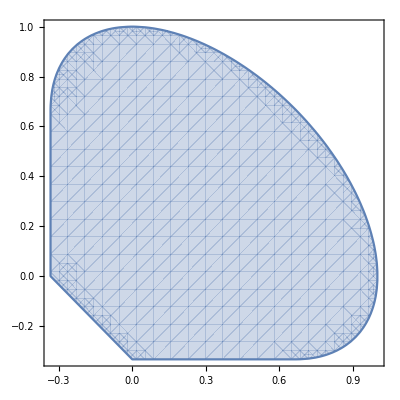

```mathematica
RegionPlot[sdpSolve[{x,y,0}]==0,{x,-1/3,1},{y,-1/3,1}]
```

```mathematica
eqs[{x_,y_,z_}]:={x,y,z}-{-1/3+1/3 (Subscript[b, 3]+Subscript[c, 6]),-1/3+1/12 (3 Subscript[b, 1]+2 √3 Subscript[b, 2]+Subscript[b, 3]+3 Subscript[c, 4]+2 √3 Subscript[c, 5]+Subscript[c, 6]),-1/3+1/36 (9 Subscript[b, 1]-6 √3 Subscript[b, 2]+3 Subscript[b, 3]+8 Subscript[c, 1]+4 √2 Subscript[c, 2]+4 √6 Subscript[c, 3]+Subscript[c, 4]+2 √3 Subscript[c, 5]+3 Subscript[c, 6])};
SDP2={Subscript[b, 1],Subscript[b, 3],Subscript[b, 1] Subscript[b, 3]-Subscript[b, 2]^2};
SDP3={Subscript[c, 1],Subscript[c, 4],Subscript[c, 6],Subscript[c, 4] Subscript[c, 6]-Subscript[c, 5]^2,Subscript[c, 1] Subscript[c, 4]-Subscript[c, 2]^2,Subscript[c, 1] Subscript[c, 6]-Subscript[c, 3]^2,-Subscript[c, 3]^2 Subscript[c, 4]+2 Subscript[c, 2] Subscript[c, 3] Subscript[c, 5]-Subscript[c, 1] Subscript[c, 5]^2-Subscript[c, 2]^2 Subscript[c, 6]+Subscript[c, 1] Subscript[c, 4] Subscript[c, 6]};
problem[{x_,y_,z_}]:={u,(#==0)&/@eqs[u{x,y,z}],Subscript[b, 1]+Subscript[b, 3]+Subscript[c, 1]+Subscript[c, 4]+Subscript[c, 6]≤4,(#>=0)&/@Flatten@{SDP2,SDP3}};
solve[{x_,y_,z_}]:=FindMaximum[problem[{x,y,z}],{u,Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6]},WorkingPrecision->50]⟦1⟧;
solve[{1,1,1}]
N[%,10]
RootApproximant@%
```

FindMaximum::sdir: Search direction has become too small.

0.55555556013888884869800222077174112200736999511719

0.5555555601

5/9

```mathematica
Clear[SDP2,problem,solve,rulesub]
rulesub[{x_,y_,z_}]:=Solve[(#==0)&/@eqs[{x,y,z}],{Subscript[b, 3],Subscript[b, 2],Subscript[b, 1]}][[1]];
SDP2={Subscript[b, 1],Subscript[b, 3],Subscript[b, 1] Subscript[b, 3]-Subscript[b, 2]^2};
SDP3={Subscript[c, 1],Subscript[c, 4],Subscript[c, 6],Subscript[c, 4] Subscript[c, 6]-Subscript[c, 5]^2,Subscript[c, 1] Subscript[c, 4]-Subscript[c, 2]^2,Subscript[c, 1] Subscript[c, 6]-Subscript[c, 3]^2,-Subscript[c, 3]^2 Subscript[c, 4]+2 Subscript[c, 2] Subscript[c, 3] Subscript[c, 5]-Subscript[c, 1] Subscript[c, 5]^2-Subscript[c, 2]^2 Subscript[c, 6]+Subscript[c, 1] Subscript[c, 4] Subscript[c, 6]};
problem[{x_,y_,z_}]:={u,Subscript[b, 1]+Subscript[b, 3]+Subscript[c, 1]+Subscript[c, 4]+Subscript[c, 6]≤4,((#>=0)&/@Flatten@{SDP2,SDP3})}/.rulesub[{x,y,z}];
solve[{x_,y_,z_}]:=FindMaximum[problem[u {x,y,z}],{u,Subscript[c, 1],Subscript[c, 2],Subscript[c, 3],Subscript[c, 4],Subscript[c, 5],Subscript[c, 6]},WorkingPrecision->50][[1]]
solve[{1,1,1}]
N[%,10]
RootApproximant@%
```

FindMaximum::sdir: Search direction has become too small.

0.55555556013888895972030468328739516437053680419922

0.5555555601

5/9

```mathematica
Clear[x,y,z]
(Flatten@{Subscript[b, 1]+Subscript[b, 3]+Subscript[c, 1]+Subscript[c, 4]+Subscript[c, 6]≤4,((#>=0)&/@Flatten@{SDP2,SDP3})}/.rulesub[{x,y,z}])[[1;;-2]];
Reduce[%,{x,y,z}];
```

{1+3 x+c_1+c_4+1/9 (9-9 x+18 y+18 z-4 c_1-2 √2 c_2-2 √6 c_3-5 c_4-4 √3 c_5)≤4,1/9 (9-9 x+18 y+18 z-4 c_1-2 √2 c_2-2 √6 c_3-5 c_4-4 √3 c_5)≥0,1+3 x-c_6≥0,-1/81 (9 √3 y-9 √3 z+2 √3 c_1+√6 c_2+3 √2 c_3-2 √3 c_4-3 c_5)^2+1/9 (9-9 x+18 y+18 z-4 c_1-2 √2 c_2-2 √6 c_3-5 c_4-4 √3 c_5) (1+3 x-c_6)≥0,c_1≥0,c_4≥0,c_6≥0,-c_5^2+c_4 c_6≥0,-c_2^2+c_1 c_4≥0,-c_3^2+c_1 c_6≥0}

```mathematica
%//Simplify
```

$Aborted

```mathematica
x=-1/3+1/12 (3 Subscript[b, 1]+2 √3 Subscript[b, 2]+Subscript[b, 3]+3 Subscript[c, 4]+2 √3 Subscript[c, 5]+Subscript[c, 6])//Expand
```

-1/3+b_1/4+b_2/(2 √3)+b_3/12+c_4/4+c_5/(2 √3)+c_6/12

```mathematica
y=-1/3+1/36 (9 Subscript[b, 1]-6 √3 Subscript[b, 2]+3 Subscript[b, 3]+8 Subscript[c, 1]+4 √2 Subscript[c, 2]+4 √6 Subscript[c, 3]+Subscript[c, 4]+2 √3 Subscript[c, 5]+3 Subscript[c, 6])//Expand
```

-1/3+b_1/4-b_2/(2 √3)+b_3/12+(2 c_1)/9+(√2 c_2)/9+1/3 √(2/3) c_3+c_4/36+c_5/(6 √3)+c_6/12

```mathematica
z=-1/3+1/3 (Subscript[b, 3]+Subscript[c, 6])//Expand
```

-1/3+b_3/3+c_6/3

```mathematica
x-z
```

b_1/4+b_2/(2 √3)-b_3/4+c_4/4+c_5/(2 √3)-c_6/4

```mathematica
z+y
```

-2/3+b_1/4-b_2/(2 √3)+(5 b_3)/12+(2 c_1)/9+(√2 c_2)/9+1/3 √(2/3) c_3+c_4/36+c_5/(6 √3)+(5 c_6)/12

```mathematica
R=RotationMatrix[ArcCos[1/√3],{1,0,0}].RotationMatrix[π/4,{0,0,1}];
R.{x1,y1,z1}
R.{-1/3+1/3 (Subscript[b, 3]+Subscript[c, 6]),-1/3+1/12 (3 Subscript[b, 1]+2 √3 Subscript[b, 2]+Subscript[b, 3]+3 Subscript[c, 4]+2 √3 Subscript[c, 5]+Subscript[c, 6]),-1/3+1/36 (9 Subscript[b, 1]-6 √3 Subscript[b, 2]+3 Subscript[b, 3]+8 Subscript[c, 1]+4 √2 Subscript[c, 2]+4 √6 Subscript[c, 3]+Subscript[c, 4]+2 √3 Subscript[c, 5]+3 Subscript[c, 6])}//Simplify//MatrixForm
```

{x1/(√2)-y1/(√2),x1/(√6)+y1/(√6)-√(2/3) z1,x1/(√3)+y1/(√3)+z1/(√3)}

(-(3 b_1+2 √3 b_2-3 b_3+3 c_4+2 √3 c_5-3 c_6)/(12 √2)
(-9 b_1+18 √3 b_2+9 b_3-16 c_1-8 √2 c_2-8 √6 c_3+7 c_4+2 √3 c_5+9 c_6)/(36 √6)
(-18+9 b_1+9 b_3+4 c_1+2 √2 c_2+2 √6 c_3+5 c_4+4 √3 c_5+9 c_6)/(18 √3))